```mathematica
SetDirectory[NotebookDirectory[]];
```

## BW fit

### Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];(*maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,0,1/2(maxx-minx),1/20}],First][[All,2]]]];*)
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];];
```

```mathematica
fitONE[input_]:=Module[{maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxis,mins,hwhmi,bad},
maxx=Max[input[[All,1]]];
minx=Min[input[[All,1]]];
maxy=Max[input[[All,2]]];
maxyx=input[[Position[input,Max[input[[All,2]]]][[1,1]],1]];
maxyi=Position[input[[All,1]],maxyx][[1,1]];
maxxy=input[[Position[input,Max[input[[All,1]]]][[1,1]],2]];
inter=Interpolation[input,InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/20}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[[All,1]],Nearest[input[[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[[maxxis[[i]]-30,2]]>input[[maxxis[[i]],2]],input[[maxxis[[i]]+30,2]]>input[[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[[All,2]],Min[input[[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input]]];,
hwhmi=Position[input,Nearest[input[[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input],maxyi+3(maxyi-hwhmi),Length[input]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input,Nearest[input[[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];];
```

### Fitting

```mathematica
uscanI={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1};
```

```mathematica
uscanI1={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10};
```

```mathematica
uscan={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100};
```

```mathematica
uscan1={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10};
```

#### Charmonium 250 MeV Perpendicular

```mathematica
Do[ccdata[n]=Import["cc_perp/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

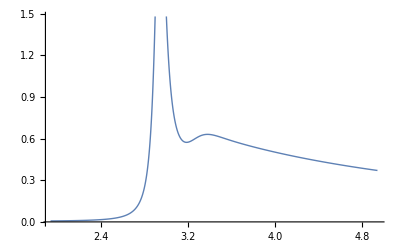

```mathematica
Block[{n=1},ListPlot[{ccdata[n]},Joined->True,PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,uscanI]];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[Γ,gfitcc,ccmodel];
store[const,cfitcc,ccmodel];
store[δbg,dfitcc,ccmodel];
store[shift,sfitcc,ccmodel];
store[shift2,s2fitcc,ccmodel];
storearea[areafitcc,ccmodel];
```

```mathematica
Transpose[{uscan,wrfitcc[[All,1]]}]
```

{{1/10,2.9376},{1/5,2.93737},{3/10,2.93698},{2/5,2.93632},{1/2,2.93526},{3/5,2.9336},{7/10,2.93081},{4/5,2.92567},{9/10,2.91427},{99/100,2.87312}}

```mathematica
Transpose[{uscan,wrfitcc[[All,2]]}]
```

{{1/10,3.26641},{1/5,3.26724},{3/10,3.26893},{2/5,3.27099},{1/2,3.27347},{3/5,3.27646},{7/10,3.27924},{4/5,3.28148},{9/10,3.29936},{99/100,3.35235}}

```mathematica
Transpose[{uscan,gfitcc[[All,2]]}]
```

{{1/10,0.337092},{1/5,0.338562},{3/10,0.340087},{2/5,0.342646},{1/2,0.346551},{3/5,0.349896},{7/10,0.354585},{4/5,0.358377},{9/10,0.361335},{99/100,0.303522}}

```mathematica
Transpose[{uscan,wrfitcc[[All,2]]}]
```

{{1/10,3.26641},{1/5,3.26724},{3/10,3.26893},{2/5,3.27099},{1/2,3.27347},{3/5,3.27646},{7/10,3.27924},{4/5,3.28148},{9/10,3.29936},{99/100,3.35235}}

```mathematica
(*gfit250cc1=gfit250cc10/.{a_,b_,c_,d_}:>{a,b,c,b-(c-b)}*)
```

#### Bottomonium 250 MeV Perpendicular

```mathematica
Do[bbdata2[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

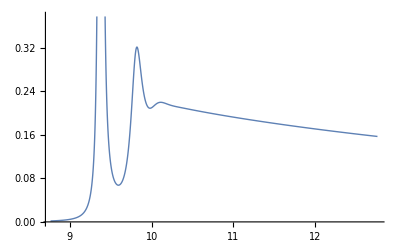

```mathematica
Block[{n=9},ListPlot[{bbdata2[n]},Joined->True,PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata2,bbmodel,uscanI]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[Γ,gfitbb,bbmodel];
store[const,cfitbb,bbmodel];
store[δbg,dfitbb,bbmodel];
store[shift,sfitbb,bbmodel];
store[shift2,s2fitbb,bbmodel];
storearea[areafitbb,bbmodel];
```

```mathematica
Transpose[{uscan,wrfitcc[[All,1]]}]
```

{{1/10,2.9376},{1/5,2.93737},{3/10,2.93698},{2/5,2.93632},{1/2,2.93526},{3/5,2.9336},{7/10,2.93081},{4/5,2.92567},{9/10,2.91427},{99/100,2.87312}}

```mathematica
Transpose[{uscan,gfitcc[[All,1]]}]
```

{{1/10,0.110791},{1/5,0.111835},{3/10,0.113703},{2/5,0.115999},{1/2,0.119018},{3/5,0.12241},{7/10,0.125835},{4/5,0.12812},{9/10,0.124459},{99/100,0.112419}}

```mathematica
Transpose[{uscan,wrfitcc[[All,2]]}]
```

{{1/10,3.26641},{1/5,3.26724},{3/10,3.26893},{2/5,3.27099},{1/2,3.27347},{3/5,3.27646},{7/10,3.27924},{4/5,3.28148},{9/10,3.29936},{99/100,3.35235}}

```mathematica
Transpose[{uscan,gfitcc[[All,2]]}]
```

{{1/10,0.337092},{1/5,0.338562},{3/10,0.340087},{2/5,0.342646},{1/2,0.346551},{3/5,0.349896},{7/10,0.354585},{4/5,0.358377},{9/10,0.361335},{99/100,0.303522}}

```mathematica
NotebookSave[];
```